-Graphics-

## Lesson 30: homogeneous linear systems

-Graphics-

## Overview

This lesson will be the first to introduce systems of differential equations.

This introduction will be limited to a simple case where every differential equation in the system is a homogeneous equation with constant coefficients.

It will follow that these systems have a number of important qualitative properties that can be described by the phase portrait of the system:

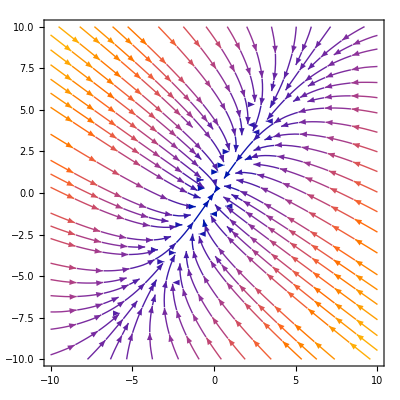

```mathematica
StreamPlot[{-3x+Sqrt[2] y,Sqrt[2]x+-2y},{x,-10,10},{y,-10,10}]
```

## Systems of Differential Equations

Initially, the focus will be on systems of the form X'=A.X, where A is an n×n constant matrix and X is a vector of variables.

As an example, a system of differential equations may take the following form:

x'(t)=x(t)+4 y(t)

y'(t)=x(t)+y(t)

The case for a 2×2 matrix is especially important because it can easily be visualized on a coordinate plane.

In addition, there are tools like direction fields that can be utilized to obtain qualitative results for the systems of equations.

## Finding Solutions

The method to find solutions involves generalizing the methods applied to second-order linear equations.

Assume the solutions are vectors of the form of exponential functions:

(a e^(r t)
b e^(r t))

Substituting this into the system gives:

ⅆ/ⅆt(a e^(r t)
b e^(r t))=A.(a e^(r t)
b e^(r t))

where A=(1 | 4
1 | 1).

Evaluating the derivative:

(a r e^(r t)
b r e^(r t))=A.(a e^(r t)
b e^(r t))

Canceling the exponential term on both sides of the equation leaves the following equation:

(a r
b r)=A.(a
b)

## Finding Solutions

This can be transformed to read:

(A-r.I).(a
b)=0

This equation is exactly the same equation used to calculate the eigenvalues of the matrix A.

Thus the vector that solves the matrix equation is a solution when r is an eigenvalue and (a
b) the associated eigenvector.

The following examples will further illustrate this technique for solving systems of differential equations.

## Example 1

Consider the following system with X=(x_1
x_2):

X'=(1 | 4
1 | 1) X

Plot the direction field and describe the qualitative behavior of solutions.

The first line of the matrix reads that:

x_1'=x_1+4 x_2

The second line reads:

x_2'=x_1+x_2

The direction field for the system can be visualized with StreamPlot:

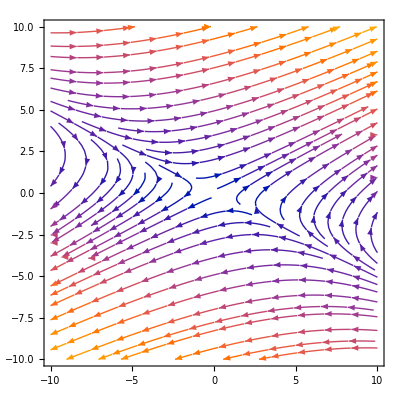

```mathematica
StreamPlot[{x1+4x2,x1+x2},{x1,-10,10},{x2,-10,10}]
```

It can be observed from the plot that solutions tend to eventually diverge from the origin.

## Example 2

Consider the system:

X'=(1 | 4
1 | 1) X

Find the general solution and draw several trajectories.

As previously shown, assume that:

X=(a
b)e^(r t)

This leads to a system of algebraic equations.

It was found that the values for r exactly correspond to the eigenvalues for the matrix (1 | 4
1 | 1):

```mathematica
A={{1,4},{1,1}};
```

```mathematica
{Subscript[λ, 1],Subscript[λ, 2]}=Eigenvalues[A]
```

{3,-1}

The values for (a
b) are the corresponding eigenvectors:

```mathematica
{v1,v2}=Eigenvectors[A]
```

{{2,1},{-2,1}}

## Example 2

Thus, the corresponding solutions of the differential equation are:

```mathematica
sol1=v1 Exp[Subscript[λ, 1] t]
```

{2 ⅇ^(3 t),ⅇ^(3 t)}

and:

```mathematica
sol2=v2 Exp[Subscript[λ, 2] t]
```

{-2 ⅇ^-t,ⅇ^-t}

The Wronskian determinant can be used to check if these functions form a fundamental solution set:

```mathematica
Wronskian[{sol1,sol2},x]
```

4 ⅇ^(2 t)

These functions form a fundamental solution set since the Wronskian determinant is never zero.

The general solution of the system is then:

```mathematica
(genSol=Subscript[C, 1] sol1+Subscript[C, 2] sol2)//MatrixForm
```

(2 ⅇ^(3 t) C_1-2 ⅇ^-t C_2
ⅇ^(3 t) C_1+ⅇ^-t C_2)

## Example 2

This solution can be solved using DSolveValue:

```mathematica
dsol=DSolveValue[{x1'[t]==x1[t]+4x2[t],x2'[t]==x1[t]+x2[t]},{x1[t],x2[t]},t]
```

{1/2 ⅇ^-t (1+ⅇ^(4 t)) C[1]+ⅇ^-t (-1+ⅇ^(4 t)) C[2],1/4 ⅇ^-t (-1+ⅇ^(4 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(4 t)) C[2]}

The arbitrary coefficients are chosen somewhat differently, but after rearranging, it can be seen that the two solutions are in fact equivalent.

Use ParametricPlot to visualize the solution curve with various choices of the arbitrary coefficients:

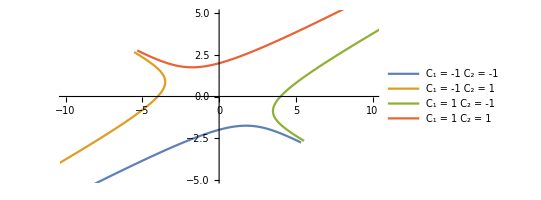

```mathematica
ParametricPlot[,{t,-1,1},]
```

## Solution Behavior

Similar to the discussion for second-order linear differential equations, there are three possibilities for the eigenvalues for A:

1. The eigenvalues are real and distinct.

When all eigenvalues are real and distinct, the eigenvectors are real and these together form the solution set for the system of differential equations.

2. Some eigenvalues are repeated.

If some eigenvalues are repeated, there is still a full set of eigenvectors. These eigenvectors and eigenvalues still form a fundamental solution set, as will be shown subsequently.

3. Some eigenvalues are complex.

Provided that there are n unique eigenvalues, there will still be solutions of the same form but with complex-valued exponents.

## Example 3

Consider the system:

X'=(0 | 1 | 2
1 | 0 | 1
2 | 1 | 0)X

Find the general solution and draw several trajectories.

As previously shown, assume that:

X=(a
b
c)e^(r t)

It was found that the values for r exactly correspond to the eigenvalues for the matrix (0 | 1 | 2
1 | 0 | 1
2 | 1 | 0):

```mathematica
A={{0,1,2},{1,0,1},{2,1,0}};
```

```mathematica
{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}=Eigenvalues[A]
```

{1+√3,-2,1-√3}

The values for (a
b
c) are the corresponding eigenvectors:

```mathematica
{v1,v2,v3}=Eigenvectors[A]
```

{{1,(2 √3)/(3+√3),1},{-1,0,1},{1,(2 √3)/(-3+√3),1}}

## Example 3

Thus the corresponding solutions of the differential equation are:

```mathematica
(sol1=Subscript[C, 1] v1 Exp[Subscript[λ, 1] t])//MatrixForm
```

(ⅇ^((1+√3) t) C_1
(2 √3 ⅇ^((1+√3) t) C_1)/(3+√3)
ⅇ^((1+√3) t) C_1)

```mathematica
(sol2=Subscript[C, 2] v2 Exp[Subscript[λ, 2] t])//MatrixForm
```

(-ⅇ^(-2 t) C_2
0
ⅇ^(-2 t) C_2)

```mathematica
(sol3=Subscript[C, 3] v3 Exp[Subscript[λ, 3] t])//MatrixForm
```

(ⅇ^((1-√3) t) C_3
(2 √3 ⅇ^((1-√3) t) C_3)/(-3+√3)
ⅇ^((1-√3) t) C_3)

The general solution of the system is then their sum:

```mathematica
(solGen=sol1+sol2+sol3)//MatrixForm
```

(ⅇ^((1+√3) t) C_1-ⅇ^(-2 t) C_2+ⅇ^((1-√3) t) C_3
(2 √3 ⅇ^((1+√3) t) C_1)/(3+√3)+(2 √3 ⅇ^((1-√3) t) C_3)/(-3+√3)
ⅇ^((1+√3) t) C_1+ⅇ^(-2 t) C_2+ⅇ^((1-√3) t) C_3)

## Example 3

Use ParametricPlot to visualize the solution for various values of C_1 and C_2:

```mathematica
ParametricPlot3D[,{t,-1,1},]
```

-Graphics3D-

## Summary

Solving systems of differential equations can largely be reduced to solving for the eigenvalues and eigenvectors.

When r is an eigenvalue and v an associated eigenvector, then there is a solution to the system of equations that takes the form v e^(r t).

The general solution is a linear combination of all eigenvectors and their eigenvalues.